## Выполнение расчетного задания по дисциплине Тепломассообмен в среде Mathematica 14 Студент: Григорьев К.А. Группа: ТФ-11-22 Задача № 3

### -Graphics-

#### Введем исходные данные:

```mathematica
d0=UnitConvert[Quantity[330,"Millimeters"],"Meters"];

r0=d0/2;L=Quantity[0.4,"Meters"];t0=Quantity[750,"DegreesCelsius"];tLiquid=Quantity[25,"DegreesCelsius"];α=Quantity[70,("Watts")/(("Meters")^2*"Kelvins")];
ρ=Quantity[2659,("Kilograms")/("Meters")^3];
cp=Quantity[871,("Joules")/("Kilograms"*"Kelvins")];
λ=Quantity[164,("Watts")/("Meters"*"Kelvins")];
τ1=UnitConvert[Quantity[1.3,"Minutes"],"Seconds"];
```

#### Найдем коэффициент температуропроводности a:

```mathematica
a=UnitConvert[N[λ/(cp*ρ)],("Meters")^2/("Seconds")]
```

0.0000708121 m^2/s

#### Числа Био по радиальному( BiRadial) и вертикальному( BiVertical) направлениям:

```mathematica
BiRadial=N[(α*r0)/λ]
```

0.0704268

```mathematica
BiVertical=N[(α*L/2)/λ]
```

0.0853659

#### Числа Фурье по радиальному( FoRadial) и вертикальному( FoVertical) направлениям:

```mathematica
FoRadial=(a*τ1)/(r0)^2
```

0.202878

```mathematica
FoVertical=(a*τ1)/(L/2)^2
```

0.138084

#### Приступим к поиску корней характеристического уравнения(MATLAB) в радиальном направлении: -Graphics- Отдельно рассмотрим седьмой корень(определим его визуально с точностью е-5) -Graphics-

```mathematica
ϵ={0.3720    ,3.8500 ,   7.0256   ,10.1804 ,  13.3290 ,  16.4749 ,  19.6195};
```

#### В вертикальном направлении: -Graphics- 7 корень: -Graphics-

```mathematica
μ={0.2881   , 3.1685    ,6.2967  ,  9.4338 ,  12.5732   ,15.7134   ,18.8541  };
```

#### Найдем функцию распределения температуры в радиальном направлении:

```mathematica
ΘRadial[r_,τ_]:=Total[(2*BesselJ[1,ϵ])/(ϵ*(BesselJ[0,ϵ]+BesselJ[1,ϵ]^2))*BesselJ[0,ϵ*r/QuantityMagnitude[r0]]*Exp[-ϵ^2*QuantityMagnitude[a]*τ/QuantityMagnitude[r0]^2]];
```

```mathematica
ΘRadial[0,0]
```

0.999048

```mathematica
tRadial[r_,τ_]=tLiquid+(t0-tLiquid)*ΘRadial[r,τ];
```

```mathematica
tLiquid+(t0-tLiquid)*ΘRadial[0,0]
```

1022.46 K

#### Найдем температуру на оси цилиндра в момент времени τ = 0 (оно тут показывает почему то 288.71288К но в расчетах далее это нормальные 1022К, можете сами прокомпилировать << tLiquid+(t0-tLiquid)*ΘRadial[0,0] >>)

```mathematica
tRadial[0,0]
```

1022.46 K

#### Нормальное tRadial[0,0]

```mathematica
tRadial[0,0]=tLiquid+(t0-tLiquid)*ΘRadial[0,0]
```

1022.46 K

```mathematica
UnitConvert[tRadial[0,0],"DegreesCelsius"]
```

749.309 °C

#### Найдем функцию распределения температуры в вертикальном направлении:

```mathematica
ΘVertical[x_,τ_]:=Total[(2*Sin[μ])/(μ+Sin[μ]*Cos[μ])*Cos[μ*x/QuantityMagnitude[L/2]]*Exp[-μ^2*(QuantityMagnitude[a]*τ)/QuantityMagnitude[(L/2)^2]]]
```

```mathematica
ΘVertical[0,0]
```

1.00022

```mathematica
tVertical[x_,τ_]:=tLiquid + (t0-tLiquid)*ΘVertical[x,τ];
```

#### Найдем температуру в центре цилиндра в момент времени τ = 0

```mathematica
tVertical[0,0]
```

1023.31 K

```mathematica
UnitConvert[tVertical[0,0],"DegreesCelsius"]
```

750.16 °C

#### Найдем функцию распределения температурного поля в цилиндре t(x,r,τ)

```mathematica
Θ3D[x_,r_,τ_]:=ΘVertical[x,τ]*ΘRadial[r,τ];
```

```mathematica
t[x_,r_,τ_]:=tLiquid + (t0-tLiquid)*Θ3D[x,r,τ];
```

#### Начнем расчет температурного поля Сначала для r=0:

```mathematica
Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}]//MatrixForm
```

(0.2 m | 694.597 °C
0.15 m | 706.261 °C
0.1 m | 713.148 °C
0.05 m | 716.469 °C
0. | 717.415 °C)

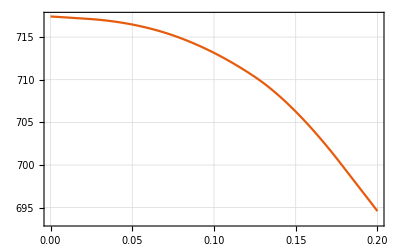

```mathematica
ListLinePlot[Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь для r=r0

```mathematica
Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[r0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}]//MatrixForm
```

(0.2 m | 671.183 °C
0.15 m | 682.438 °C
0.1 m | 689.085 °C
0.05 m | 692.289 °C
0. | 693.202 °C)

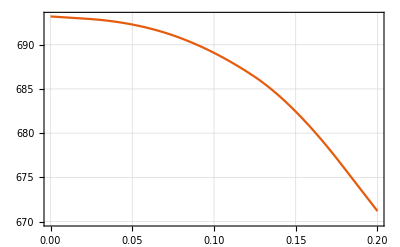

```mathematica
ListLinePlot[Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[r0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь для x=0

```mathematica
Table[{ N[r],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}]//MatrixForm
```

(0.165 m | 693.202 °C
0.12375 m | 703.598 °C
0.0825 m | 711.193 °C
0.04125 m | 715.845 °C
0. | 717.415 °C)

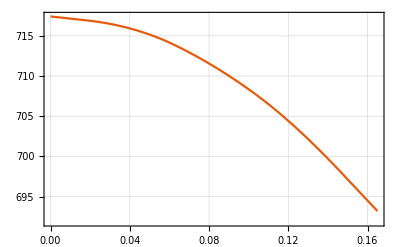

```mathematica
ListLinePlot[Table[{ N[r],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь для x=L/2

```mathematica
Table[{ N[r],UnitConvert[t[QuantityMagnitude[L/2],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}]//MatrixForm
```

(0.165 m | 671.183 °C
0.12375 m | 681.236 °C
0.0825 m | 688.581 °C
0.04125 m | 693.079 °C
0. | 694.597 °C)

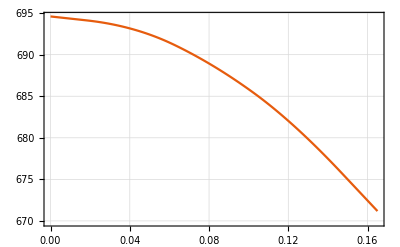

```mathematica
ListLinePlot[Table[{ N[r],UnitConvert[t[QuantityMagnitude[L/2],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Покажем распределение температуры в центре цилиндра и на расстоянии 0.2 d_0 от поверхности как функцию времени Сначала для центра:

```mathematica
Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[8]}]//MatrixForm
```

(78. s | 717.415 °C
156. s | 692.348 °C
234. s | 666.973 °C
312. s | 642.21 °C
390. s | 618.314 °C
468. s | 595.322 °C
546. s | 573.215 °C
624. s | 551.964 °C)

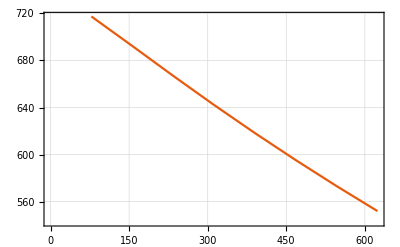

```mathematica
ListLinePlot[Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[8]}],PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь на расстоянии 0.2 d_0 (0.4 r_0)от поверхности , следовательно r=0.6 r_0)

```mathematica
Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0.6*r0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[8]}]//MatrixForm
```

(78. s | 708.5 °C
156. s | 684.047 °C
234. s | 659.002 °C
312. s | 634.547 °C
390. s | 610.948 °C
468. s | 588.241 °C
546. s | 566.409 °C
624. s | 545.421 °C)

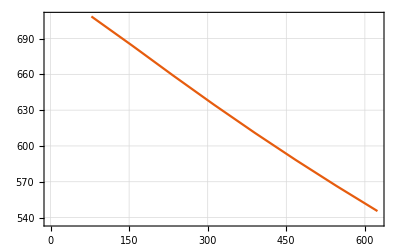

```mathematica
ListLinePlot[Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0.6*r0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[8]}],PlotTheme->"Scientific",GridLines->Automatic]
```

#### Для определения темпа охлаждения и коэффициента температуропроводности заготовки построит несколько зависимостей ln(θ) используя данные полученные выше( в центре и на 0.6r_0). θ = t-tLiquid

```mathematica
lnForCenter=Table[{ N[k*τ1],Log[QuantityMagnitude[UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]-tLiquid]]},{k,Range[8]}]
```

{{78. s,6.54018},{156. s,6.50331},{234. s,6.46455},{312. s,6.42521},{390. s,6.38572},{468. s,6.3462},{546. s,6.30667},{624. s,6.26713}}

```mathematica
lnForPoint6r0=Table[{ N[k*τ1],Log[QuantityMagnitude[UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0.6*r0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]-tLiquid]]},{k,Range[8]}]
```

{{78. s,6.52723},{156. s,6.49079},{234. s,6.45205},{312. s,6.41272},{390. s,6.37323},{468. s,6.33371},{546. s,6.29417},{624. s,6.25464}}

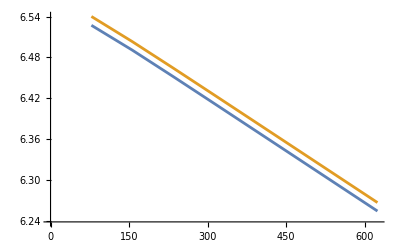

```mathematica
ListLinePlot[{lnForPoint6r0,lnForCenter}]
```

#### Нетрудно заметить,что стадии. регулярного режима гарантированно соответствует интервал [200,600] s. Найдем число Фурье в краевых точках интервала регулярного режима и удостоверимся что оно больше 0.3

```mathematica
FoRadialAt200=(a*Quantity[200,"Seconds"])/r0^2
```

0.520199

```mathematica
FoRadialAt600=(a*Quantity[600,"Seconds"])/r0^2
```

1.5606

```mathematica
FoVerticalAt200=(a*Quantity[200,"Seconds"])/(L/2)^2
```

0.35406

```mathematica
FoVerticalAt600=(a*Quantity[600,"Seconds"])/(L/2)^2
```

1.06218

#### Приступим к поиску темпа охлаждения m для наших двух точек

```mathematica
mAtCenter=Log[Θ3D[0,0,200]/Θ3D[0,0,600]]/Quantity[600-200,"Seconds"]
```

0.000505664 per second

```mathematica
mAtPoint6r0=Log[Θ3D[0,QuantityMagnitude[0.6*r0],200]/Θ3D[0,QuantityMagnitude[0.6*r0],600]]/Quantity[600-200,"Seconds"]
```

0.000505653 per second

#### Берем среднее

```mathematica
m=(mAtCenter+mAtPoint6r0)/2
```

0.000505658 per second

#### Fo > 0.3 поэтому ряд Фурье сходится быстро и первый член достаточно описывает все решение. Найдем коэффициент формы K:

```mathematica
K=1/((First[ϵ]/r0)^2+(First[μ]/(L/2))^2)
```

0.139704 m^2

#### Найдем коэффициент температуропроводности по второй теореме Кондратьева(допущение что наше m=m_∞) и сравним с теоретическим:

```mathematica
aExperimental=K*m
```

0.0000706422 m^2/s

```mathematica
a
```

0.0000708121 m^2/s

```mathematica
δa=Abs[a-aExperimental]/a
```

0.00239884

#### Найдем количество теплоты, отданное цилиндром за время τ_1: Для начала найдем сколько теплоты он отдаст до того момента как Θ==1 т.е. t=tLiquid

```mathematica
Q=N[π*(r0)^2*L*ρ*cp*(t0-tLiquid)]
```

5.7445×10^7 J

```mathematica
ΘRadialAverage=Total[(4*BiRadial^2)/(ϵ^2*(ϵ^2+BiRadial^2))*Exp[-ϵ^2*FoRadial]]
```

0.972479

```mathematica
ΘVerticalAverage=Total[(2*Sin[μ]^2)/(μ^2+μ*Sin[μ]*Cos[μ])*Exp[-μ^2*FoVertical]]
```

0.988486

```mathematica
ΘAverage=ΘVerticalAverage*ΘRadialAverage
```

0.961282

```mathematica
Qτ1=Q(1-ΘAverage)
```

2.22415×10^6 J

#### Подытожим полным температурным полем в момент времени τ_1

```mathematica
Show[ListLinePlot3D[Table[t[QuantityMagnitude[x],QuantityMagnitude[r],QuantityMagnitude[τ1]],{x,0,L/2,L/4},{r,0,r0,r0/4}]],Boxed->False]
```

-Graphics3D-

```mathematica
data=Flatten[Table[{x,r,t[QuantityMagnitude[x],QuantityMagnitude[r],QuantityMagnitude[τ1]]},{x,0,L/2,L/4},{r,0,r0,r0/4}],1];

ListPlot3D[data,Boxed->True,Mesh->None,PlotStyle->Directive[Opacity[0.7],Yellow],AxesLabel->{"x (m)","r (m)","t (°C)"},LabelStyle->Directive[Medium,Black],InterpolationOrder->4]
```

-Graphics3D-

#### (покрутите поверхность :_) )